```mathematica
nprey = 12;
mu = {-15.5,-17.5,-15.6,-15.5,-14.3,-15.4,-16.0,-17.0,-15.8,-13.3,-17.5,-16.2};
sig = {1.0,0.9,0.7,0.9,0.9,0.9,0.5,1.1,0.8,1.1,1.4,1.0};
VarOtter=
ParallelTable[
Table[
Dparam =Table[1,{nprey}];
Dparam[[prey1]] = a;

a0 = Total[Dparam];

VarZ=N[Sum[Dparam[[i]]/a0(sig[[i]]^2+mu[[i]]^2) - (Dparam[[i]]^2 *mu[[i]]^2)/a0^2,{i,1,nprey}] - Sum[(Dparam[[i]]*Dparam[[j]]*mu[[i]]*mu[[j]])/a0^2 Boole[i≠j],{i,1,nprey},{j,1,nprey}]];
propi = a/a0;
{propi,0.15*VarZ/2},
{a,1,1000,1}],
{prey1,1,nprey,1}];
```

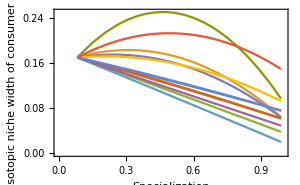

```mathematica
VarOtterPlot=ListPlot[VarOtter,PlotRange->{{0,1},All},Joined->True,PlotStyle->ColorData[97],Frame->True,
FrameLabel->{"Specialization","Isotopic niche width of consumer diet"},AxesOrigin->{0,0},ImageSize->300]
```

```mathematica
VarZs=(1-s)/(n-1)*A + s*B - ((1-s)/(n-1)*c + s*d)^2;
Ds = D[VarZs,s];
Ssol2 = s/.FullSimplify[Solve[Ds==0,s]]
mu = {-15.5,-17.5,-15.6,-15.5,-14.3,-15.4,-16.0,-17.0,-16,-13.3,-17.5,-16.2};
sig = {1.0,0.9,0.7,0.9,0.9,0.9,0.5,1.1,0.8,1.1,1.4,1.0};
nprey = Length[mu];
SeaOtterInversions=
Table[
FullSsol = Ssol2/.{
n->nprey,
A->Sum[(sig[[i]]^2 + mu[[i]]^2)Boole[i≠prey1],{i,1,nprey}],
B->(sig[[prey1]]^2 + mu[[prey1]]^2),
c->Sum[mu[[i]]Boole[i≠prey1],{i,1,nprey}],
d-> mu[[prey1]]
};
PreyOffset = Abs[Mean[mu]-mu[[prey1]]];
Flatten[{N[FullSsol],PreyOffset},1],
{prey1,1,nprey,1}];
```

{(A+B (-1+n)^2-A n+2 c (c+d-d n))/(2 (c+d-d n)^2)}

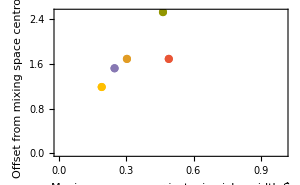

```mathematica
InversionPlot=
ListPlot[Partition[SeaOtterInversions,1],PlotStyle->ColorData[97],PlotRange->{{0,1},All},Frame->True,FrameLabel->{"Maximum consumer isotopic niche width Ŝ","Offset from mixing space centroid"},ImageSize->300(*,
PlotLegends->{"Clams","Mussels","Worms","Abalone","Snails","R.Crabs","D.Crabs","P.Urchins","R.Urchins","K.Crabs","Sea Stars","S.Crabs"}*)]
```

```mathematica
OtterPlot=Grid[{{
VarOtterPlot,
InversionPlot,
SwatchLegend[Table[ColorData[97,i],{i,1,12}],{"Clams","Mussels","Worms","Abalone","Snails","R.Crabs","D.Crabs","P.Urchins","R.Urchins","K.Crabs","Sea Stars","S.Crabs"},LegendFunction->None,LegendMargins->1,LegendLayout->{"Column",2},LegendMarkers->"Bubble",ImageSize->125]
}}]
```

-Graphics- | -Graphics- |

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_ottervar.pdf",OtterPlot]
```

/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_ottervar.pdf